```mathematica
SizedDots[n_]:= Table[ Directive[PointSize[0.05*(n+1-i)/n],Hue[i/n]],{i,n}]
```

# Novel Map

## New Map and Attractor

I added one term to the Henon map to see what happens

```mathematica
F[a_,b_,c_][{x_,y_}]:={1- a x^2 + y, x (b+c  y)}
DF[a_,b_,c_][{x_,y_}]:={{-2 a x,1},{b+c y,c x}}
```

Our target is to start to understand the behavior of this system.  Note, if c=0 we have the Henon system.

## Parametric Dependence: Visual Exploration.

Lets try to get a feel for what it does. It is hard to see what happens in the Phase Space

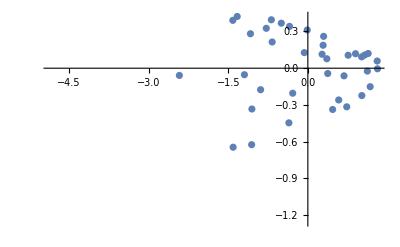

```mathematica
MaxIter=12345; MaxRad=10^2;
{a,b,c}={1.4,0.3,0.4};
Data=NestWhileList[F[a,b,c],{0.21,0.3},Norm[#]<MaxRad&,1,MaxIter]⟦10;;-1⟧;
ListPlot[Data]
```

It may easier to see what is going on with “time” included.

```mathematica
MaxIter=12345; MaxRad=10^2;
{a,b,c}={1.1,0.3,0.4};
Data=NestWhileList[F[a,b,c],{0.21,0.3},Norm[#]<MaxRad&,1,MaxIter];TabView[{
"x_1"->ListPlot[ Data⟦All,1⟧,AxesLabel->{"k","x_1"}],
"x_2"->ListPlot[ Data⟦All,2⟧,AxesLabel->{"k","x_2"}]
}]
```

12